```mathematica
Grad[r^2*Cos[2*θ],{r,θ,z},"Cylindrical"]
```

{2 r Cos[2 θ],-2 r Sin[2 θ],0}

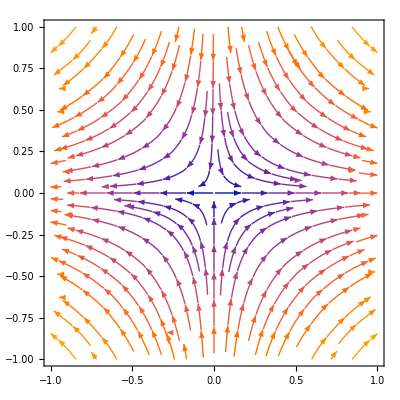

```mathematica
StreamPlot[Evaluate[TransformedField["Polar"->"Cartesian",{2*r*Cos[2 θ],-2*r* Sin[2 θ]},{r,θ}->{x,y}]],{x,-1,1},{y,-1,1}]
```

```mathematica
Grad[r^4*Cos[4*θ],{r,θ,z},"Cylindrical"]
```

{4 r^3 Cos[4 θ],-4 r^3 Sin[4 θ],0}

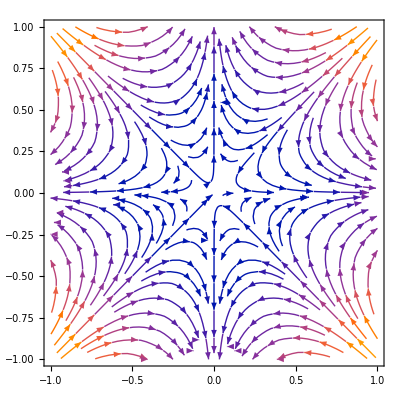

```mathematica
StreamPlot[Evaluate[TransformedField["Polar"->"Cartesian",{4 r^3 Cos[4 θ],-4 r^3 Sin[4 θ]},{r,θ}->{x,y}]],{x,-1,1},{y,-1,1}]
```

```mathematica
Grad[r^(2/3)*Cos[2*θ/3],{r,θ,z},"Cylindrical"]
```

{(2 Cos[(2 θ)/3])/(3 r^(1/3)),-(2 Sin[(2 θ)/3])/(3 r^(1/3)),0}

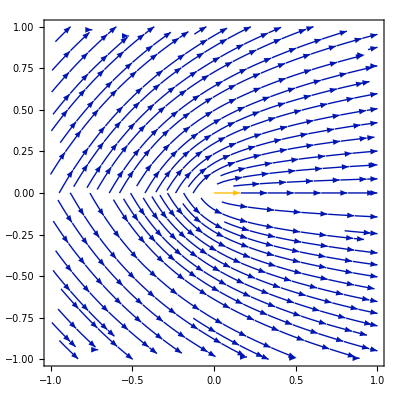

```mathematica
StreamPlot[Evaluate[TransformedField["Polar"->"Cartesian",{(2 Cos[(2 θ)/3])/(3 r^(1/3)),-(2 Sin[(2 θ)/3])/(3 r^(1/3))},{r,θ}->{x,y}]],{x,-1,1},{y,-1,1}]
```

```mathematica
ψ=(2/3)*r^(3/2)*Sin[3θ/2];
```

```mathematica
ur=(1/r)*D[ψ,θ]
```

√r Cos[(3 θ)/2]

```mathematica
uθ=-D[ψ,r]
```

-√r Sin[(3 θ)/2]

```mathematica
Grad[(2/3)r^(3/2)*Cos[3*θ/2],{r,θ,z},"Cylindrical"]
```

{√r Cos[(3 θ)/2],-√r Sin[(3 θ)/2],0}

```mathematica
D[D[Integrate[f[r-cs*t],t],t],t]
```

-cs f'[r-cs t]

```mathematica
D[D[Integrate[f'[r-cs*t],t],t],t]
```

-cs f''[r-cs t]

```mathematica
F=(1/(ρ*r^2)*Integrate[f[r-cs*t],t])-(1/(ρ*r))*Integrate[f'[r-cs*t],t];
```

```mathematica
cs^2*(1/r^2)*D[r^2*D[F,r],r]-2*cs^2/r^2*F//FullSimplify
```

(cs (-f'[r-cs t]+r f''[r-cs t]))/(r^2 ρ)

```mathematica
MatrixRank[{{0, 1,1,1,2},{-1, 0,0,-1,-1}}]
```

2

```mathematica
MatrixRank[{{1,0,0,0,1,1,0},{1,1,1,0,-3,-1,1},{-2,-1,0,-1,0,-1,-1}}]
```

3

```mathematica
MatrixRank[{{1,0,0,0,1,1},{1,1,1,0,-3,-1},{-2,-1,0,-1,0,-1}}]
```

3

```mathematica
DSolve[vz'[r]+r*vz''[r]==0,vz[r],r]
```

{{vz[r]→C[2]+C[1] Log[r]}}

```mathematica
VZ=u/(Log[R2/R1])*(Log[r/R1])//FullSimplify
```

(u Log[r/R1])/Log[R2/R1]

```mathematica
D[VZ,r]//FullSimplify
```

u/(r Log[R2/R1])

```mathematica
TrigToExp[DSolve[r*D[r*D[R[r],r],r]==λ^2*R[r],R[r],r]]
```

{{R[r]→(r^-λ C[1])/2+(r^λ C[1])/2-1/2 ⅈ r^-λ C[2]+1/2 ⅈ r^λ C[2]}}

```mathematica
TrigToExp[DSolve[R''[r] +R'[r]/r-λ^2/r^2*R[r]==0,R[r],r]]
```

{{R[r]→(r^-λ C[1])/2+(r^λ C[1])/2-1/2 ⅈ r^-λ C[2]+1/2 ⅈ r^λ C[2]}}

```mathematica
Grad[u*r*(1+R^2/r^2)*Cos[θ],{r,θ,z},"Cylindrical"]//FullSimplify
```

{(1-R^2/r^2) u Cos[θ],-((1+R^2/r^2) u Sin[θ]),0}

```mathematica
vr=D[u*r*(1+R^2/r^2)*Cos[θ],r]//FullSimplify
```

(1-R^2/r^2) u Cos[θ]

```mathematica
vθ=(1/r)*D[u*r*(1+R^2/r^2)*Cos[θ],θ]//FullSimplify
```

-((1+R^2/r^2) u Sin[θ])

```mathematica
vr^2+vθ^2/.{r->R}//FullSimplify
```

4 u^2 Sin[θ]^2

```mathematica
u^2-4 u^2 Sin[θ]^2//FullSimplify
```

u^2 (-1+2 Cos[2 θ])

```mathematica
Sqrt[vr^2+vθ^2]//FullSimplify
```

√((u^2 (r^4+R^4-2 r^2 R^2 Cos[2 θ]))/r^4)

```mathematica
vxy=TransformedField["Polar"->"Cartesian",{(1-R^2/r^2) u Cos[θ],-((1+R^2/r^2) u Sin[θ])},{r,θ}->{x,y}]//FullSimplify
```

{u+(R^2 u (-x^2+y^2))/((x^2+y^2)^2),-(2 R^2 u x y)/((x^2+y^2)^2)}

```mathematica
vxy[[2]]/vxy[[1]]/.{x->Sqrt[R^2/(1-K/y)-y^2]}//FullSimplify
```

-(2 (K-y)^2 √(y (-y+R^2/(-K+y))))/(2 K^2 y+2 y^3+K (R^2-4 y^2))

```mathematica
1/D[Sqrt[R^2/(1-K/y)-y^2],y]//FullSimplify
```

-(2 √(y (-y+R^2/(-K+y))))/((K R^2)/(K-y)^2+2 y)

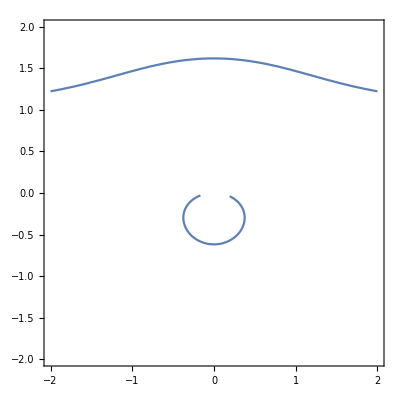

```mathematica
ContourPlot[x^2+y^2==1/(1-1/y),{x,-2,2},{y,-2,2}]
```